```mathematica
Series[Sqrt[1-H^2], {H, H0, 1}]
```

√(1-H0^2)-(H0 (H-H0))/(√(1-H0^2))+O[H-H0]^2

```mathematica
Series[Sin[2ArcSin[H]],{H,H0,1}]
```

Sin[2 ArcSin[H0]]+(2 Cos[2 ArcSin[H0]] (H-H0))/(√(1-H0^2))+O[H-H0]^2

```mathematica
Series[Cos[2ArcSin[H]],{H,H0,1}]
```

Cos[2 ArcSin[H0]]-(2 Sin[2 ArcSin[H0]] (H-H0))/(√(1-H0^2))+O[H-H0]^2

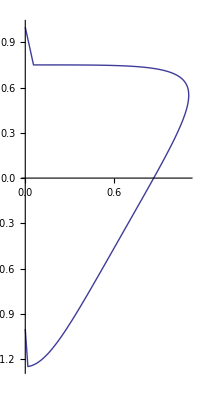

```mathematica
ParametricPlot[
{Sqrt[1-H^2](1+1/2 H),
H(1+1/2Sqrt[1-H^2]Cot[2ArcSin[H]])},
{H, -1, 1}]
```

```mathematica
sin:=Sin[2ArcSin[H]]
```

```mathematica
cos:=Cos[2ArcSin[H]]
```

```mathematica
w:= Sqrt[1-H^2]
```

```mathematica
set = {t(sin + s dH cos /w ) + s(-sin) == H dH / w,t(cos-2 dH/w sin)+s(-cos)==0}
```

{-s Sin[2 ArcSin[H]]+t ((dH s Cos[2 ArcSin[H]])/(√(1-H^2))+Sin[2 ArcSin[H]])==(dH H)/(√(1-H^2)),-s Cos[2 ArcSin[H]]+t (Cos[2 ArcSin[H]]-(2 dH Sin[2 ArcSin[H]])/(√(1-H^2)))==0}

```mathematica
Solve[set, {s, t}]
```

{{s→Sec[2 ArcSin[H]] (-Cos[2 ArcSin[H]]^2/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])+(H^2 Cos[2 ArcSin[H]]^2)/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])+(Cos[2 ArcSin[H]] Cos[6 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])-(H^2 Cos[2 ArcSin[H]] Cos[6 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])+(dH √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH H^2 √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH H^2 √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(6 dH √(1-H^2) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])-(dH √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH H^2 √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH H^2 √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(6 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]]^2)/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(6 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]]^2)/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(2 dH √(1-H^2) Cos[2 ArcSin[H]] Sin[6 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])-(2 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]] Sin[6 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(2 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]] Sin[6 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(Cos[2 ArcSin[H]] √(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH √(-(-1+H) (1+H)) Sin[2 ArcSin[H]] √(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH √(-(-1+H) (1+H)) Sin[2 ArcSin[H]] √(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))),t→(-2 Cos[2 ArcSin[H]]+2 H^2 Cos[2 ArcSin[H]]+2 Cos[6 ArcSin[H]]-2 H^2 Cos[6 ArcSin[H]]-12 dH √(1-H^2) Sin[2 ArcSin[H]]+4 dH √(1-H^2) Sin[6 ArcSin[H]]+√(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))},{s→Sec[2 ArcSin[H]] (-Cos[2 ArcSin[H]]^2/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])+(H^2 Cos[2 ArcSin[H]]^2)/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])+(Cos[2 ArcSin[H]] Cos[6 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])-(H^2 Cos[2 ArcSin[H]] Cos[6 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])+(dH √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH H^2 √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH H^2 √(-(-1+H) (1+H)) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(6 dH √(1-H^2) Cos[2 ArcSin[H]] Sin[2 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])-(dH √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH H^2 √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(dH √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH H^2 √(-(-1+H) (1+H)) Cos[6 ArcSin[H]] Sin[2 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(6 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]]^2)/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(6 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]]^2)/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(2 dH √(1-H^2) Cos[2 ArcSin[H]] Sin[6 ArcSin[H]])/(3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]])-(2 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]] Sin[6 ArcSin[H]])/((1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(2 dH^2 √(-(-1+H) (1+H)) √(1-H^2) Sin[2 ArcSin[H]] Sin[6 ArcSin[H]])/((1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))-(Cos[2 ArcSin[H]] √(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH √(-(-1+H) (1+H)) Sin[2 ArcSin[H]] √(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (1-H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))+(dH √(-(-1+H) (1+H)) Sin[2 ArcSin[H]] √(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (1+H) (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))),t→(-2 Cos[2 ArcSin[H]]+2 H^2 Cos[2 ArcSin[H]]+2 Cos[6 ArcSin[H]]-2 H^2 Cos[6 ArcSin[H]]-12 dH √(1-H^2) Sin[2 ArcSin[H]]+4 dH √(1-H^2) Sin[6 ArcSin[H]]-√(-4 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]) (-2 H+2 H^3-2 H Cos[4 ArcSin[H]]+2 H^3 Cos[4 ArcSin[H]]-4 dH H √(1-H^2) Sin[4 ArcSin[H]])+(2 Cos[2 ArcSin[H]]-2 H^2 Cos[2 ArcSin[H]]-2 Cos[6 ArcSin[H]]+2 H^2 Cos[6 ArcSin[H]]+12 dH √(1-H^2) Sin[2 ArcSin[H]]-4 dH √(1-H^2) Sin[6 ArcSin[H]])^2))/(2 (3 Cos[2 ArcSin[H]]-4 dH^2 Cos[2 ArcSin[H]]-3 H^2 Cos[2 ArcSin[H]]+Cos[6 ArcSin[H]]+4 dH^2 Cos[6 ArcSin[H]]-H^2 Cos[6 ArcSin[H]]))}}

```mathematica
Cot[2ArcSin[H]]
```

Cot[2 ArcSin[H]]

```mathematica
Simplify[%]
```

Cot[2 ArcSin[H]]

```mathematica
Series[1/(2w) + Y Cot[2 ArcSin[H]], {H, H0, 1}]
```

(1/(2 √(1-H0^2))+Y Cot[2 ArcSin[H0]])+(H0/(2 (1-H0^2)^(3/2))-(2 Y)/(√(1-H0^2))-(2 Y Cot[2 ArcSin[H0]]^2)/(√(1-H0^2))) (H-H0)+O[H-H0]^2

```mathematica
Y[H_]:=H/(2(1-H^2)(2+Cot[2ArcSin[H]]^2))
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

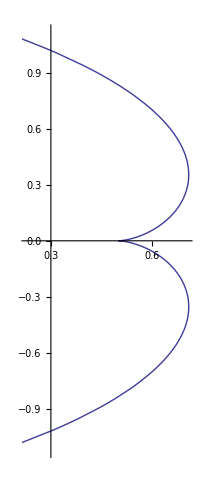

```mathematica
ParametricPlot[{1/(2Sqrt[1-H^2]) +Y[H]Cot[2ArcSin[H]],Y[H]},{H, -1, 1}]
```